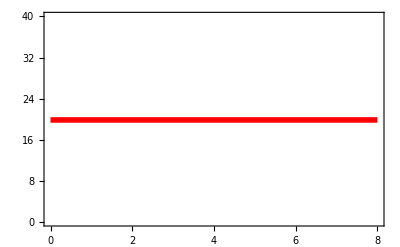
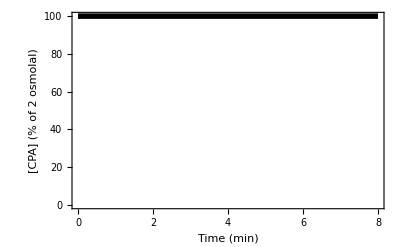
-Graphics--Graphics-CPA Exposure Profile 1

-Graphics-

```mathematica
(*Goal: Benchmark my simulation using result from Kleinhans 1998*)
(*Conclusion: I can replicate the published result if I use a value of partial molar CPA volume that is 1000x too high (I think Kleinhans made a conversion error)*)

Clear["Global`*"]

(*inputs*)
profiles={
{{{100,t<8*60}},293,1}
}; (*enter in the format: {surroudning CPA concentration as a function of time (c=f(t)), temperature (T), step number of the final loading step (locLf)}*)
Mmax=2; (*osmol/kg, max osmolality of CPA surrounding the sample*)
MVCPA=71/1000; (*m^3/mol, molar volume of CPA, compare to 7.1E-5 m^3/mol for glycerol, compare to 7.1E-5 m^3/mol for DMSO*)
Mne=.3; (*osmol/kg, extracellular nonpenetrating osmolality, compare to .335 for Celsior (Ostrozka-Cieslik 2009)*)
Vb=.25*V0; (*osmotically inactive cell volume, compare to .2V0 for oocytes (Newton 1999)*)
adhered=0; (*enter 1 if cell is adherent (2D), enter ≠ 1 if cell is nonadherent (3D)*)

(*geometry-dependent inputs and calculations (comment out the geometry that you do not want)*)
(*(*inputs for an elliptical geometry*)
Lcell=110/1000/1000; (*m, length of cell, compare to 110 um for rat ventricular myocytes (Boyett 1991)*)
R1cell = 25/1000/1000; (*m, major radius of cell, compare to 25 um for rat ventricular myocytes (Boyett 1991)*)
RRatio=1/3; (*ratio of minor radius to major radius, compare to 1/3 for rat ventricular myocytes (Boyett 1991)*)
(*equations for an elliptical geomtery*)
R2cell=R1cell*RRatio; (*m, minor radius of cell*)
A0=π*Lcell*(R1cell+R2cell)+2*π*R1cell*R2cell; (*m^2, initial cell surface area, compare to 4.5E-6 for oocytes (Carbrey)*)
V0=π*Lcell*R1cell*R2cell/4; (*m^3, initial cell volume*)*)
(*inputs for a spherical geometry*)
Dcell=100/1000/1000; (*m, cell diameter, compare to 20 um for mostly-detached D13 hiPSC-CM (my measurement)*)
(*equations for a spherical geometry*)
A0=π*Dcell^2; (*m^2, initial cell surface area, compare to 4.5E-6 for oocytes (Carbrey)*)
V0=π*Dcell^3/6; (*m^3, initial cell volume*)

(*constants*)
Rgas=8.3145; (*J/mol/K = N*m/mol/K = kg*m^2/mol/K/s^2, gas constant*)

(*parameters*)
M0=0; (*osmol/kg, initial intracellular CPA osmolality*)
Mn0=.3; (*osmol/kg, initial intracellular nonpenetrating osmolality*)
Lp=1.05/1000/60/101325; (*m^2*s/kg = m/s/Pa*)
Ps=.00406/100/60; (*m/s*)

(*equations*)
If[adhered==1, (*if cell is adhered*)
A0=A0/2; (*assume half the cell membrane is exposed*)
]

(*initialization*)
VPlots={};
colors={Blue,Green,Black, Red,Purple,Orange,Brown,Yellow};
table={{"Profile","Max M_e (osmolal)","T (°C)","t_tot (min)","Min V/V_0","Max V/V_0"}};

(*execution*)
nProfiles=Length[profiles];
ttotmax=Max[profiles[[All,1]][[All,-1]][[All,2,2]]];
For[i=1,i<nProfiles+1,i++,
Me=Piecewise[profiles[[i]][[1]]]*Mmax/100; (*mol/m^3 = mM, c=f(t)*)
T=profiles[[i]][[2]]; (*K, T=f(t)*)
locLf=profiles[[i]][[3]]; (*location of the final loading step*)
nSteps=Length[profiles[[i]][[1]]];(*number of c steps*)
ttot=Last[profiles[[i]][[1]]][[2,2]]; (*s, total simulation time*)
vnSol=NDSolve[{v'[t]==-Lp*A0*Rgas*T*(Mne+Me-(Mn0*(V0-Vb))/v[t]-n[t]/v[t]),n'[t]==Ps*A0*(Me-n[t]/v[t]),v[0]==V0-Vb,n[0]==M0*(V0-Vb)},{v,n},{t,0,ttot},MaxStepSize->.1][[1]];
v[t_]:=Evaluate[v[t]/.vnSol[[1]]]; (*m^3, volume of intracellular water*)
n[t_]:=Evaluate[n[t]/.vnSol[[2]]];(*osmol = mol (equation true for CPA), amount of intracellular CPA*)
Vr[n_,v_]:=(v+MVCPA*n+Vb)/V0;(*ratio of cell volume to initial cell volume*)
(*initialization*)
Vmins={}; (*list of Vmin for each step*)
Vmaxs={}; (*list of Vmax for each step*)
tPriorSteps=0; (*s, time of all prior steps*)
For[j=1,j<nSteps+1,j++,
tCurrentStep=profiles[[i]][[1]][[j]][[2,2]]; (*s, time until the end of the current step*)
If[j≤locLf,(*if this is a loading step*)
AppendTo[Vmins,FindMinimum[{Vr[n[t],v[t]],tPriorSteps<t<tCurrentStep},t][[1]]];
,(*if this is an unloading step*)
AppendTo[Vmaxs,FindMaximum[{Vr[n[t],v[t]],tPriorSteps<t<tCurrentStep},t][[1]]];
];
tPriorSteps=tCurrentStep;
];
Vmin=If[Length[Vmins]>0,Min[Vmins],Min[{Vr[n[0],v[0]],Vr[n[ttot],v[ttot]]}]];
Vmax=If[Length[Vmaxs]>0,Max[Vmaxs],Max[{Vr[n[0],v[0]],Vr[n[ttot],v[ttot]]}]];
Me=Me/.t->t*60; (*for plotting in min*)
Print[Labeled[Overlay[{Plot[T-273.15,{t,0,ttot/60},PlotStyle->{Red,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,40},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Red},FrameLabel->{{None,"T (°C)"},{None,None}}],Plot[Me*100/Mmax,{t,0,ttot/60},PlotStyle->{Black,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,100},Frame->{True,True,False,False},FrameStyle->{Automatic,Black,Automatic,Automatic},FrameLabel->{{"[CPA] (% of "<>ToString[NumberForm[Mmax,2]]<>" osmolal)",None},{"Time (min)",None}}]}],"CPA Exposure Profile "<>ToString[i],Top]];
If[i<nProfiles,(*if this is not the last profile*)
AppendTo[VPlots,Plot[Vr[n[t*60],v[t*60]],{t,0,ttotmax/60},PlotRange->{0,Ceiling[1.1*Vmax,.1]},AxesLabel->{"t (min)","V/V_0"},PlotStyle->colors[[i]]]];
,(*if this is the last profile*)
AppendTo[VPlots,Plot[Vr[n[t*60],v[t*60]],{t,0,ttotmax/60},PlotRange->{0,Ceiling[1.1*Vmax,.1]},AxesLabel->{"t (min)","V/V_0"},PlotStyle->colors[[i]],PlotLegends->Placed[LineLegend[colors,Range[nProfiles],LegendLabel->"Profile",LegendFunction->Framed],{1,.6}]]];
];
AppendTo[table,{i,NumberForm[Mmax,2],T-273.15,ttot/60,Round[Vmin,.01],Round[Vmax,.01]}];
Clear[v,n];
]; (*end of i loop*)
Show[VPlots]
Dataset[AssociationThread[First@table->#]&/@Rest@table]
```